```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/nfs/dmj/2023/pr459797/Dokumenty/Wolfram Mathematica

```mathematica
data=Import["zad3.txt", "Data"]
```

{{0.529555,1.30622},{1.04967,0.534644},{1.50017,-0.163582},{2.00208,0.684752},{2.51418,2.0856},{3.00022,1.6303},{3.51966,0.778942},{4.07291,1.53728},{4.58433,2.78182},{5.09847,2.7129},{5.53623,1.56204},{6.01164,1.96681},{6.5588,3.59588},{7.01677,3.86335},{7.56395,2.51955},{8.01177,2.32758},{8.59206,4.12716},{9.08513,4.66276},{9.56061,3.61301},{10.0818,3.1612},{10.5961,4.76559},{11.0808,5.43314},{11.5106,4.69323},{12.0773,3.87455},{12.5423,5.09203},{13.024,6.34455},{13.5991,5.60987},{14.0543,4.84901},{14.5923,5.6796},{15.0792,7.15937},{15.5704,6.75874},{16.0093,5.78583},{16.5814,6.15322},{17.0303,7.84135},{17.5736,7.83023},{18.009,6.7027},{18.5162,6.56556},{19.0905,8.44182},{19.5609,8.70892},{20.0827,7.64239},{20.5753,7.44133},{21.0451,8.87238},{21.5688,9.69194},{22.0464,8.89157},{22.5325,8.09328},{23.0909,9.47801},{23.523,10.5738},{24.0876,9.79803},{24.5937,8.97476},{25.0927,10.1316}}

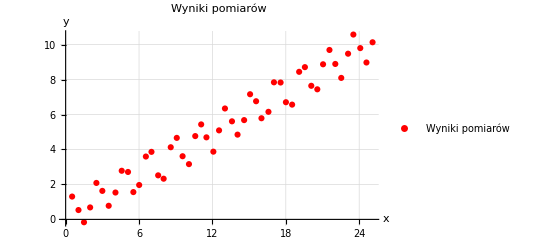

```mathematica
plotData=ListPlot[data,PlotStyle->{Red}, AxesLabel->{x, y}, PlotLabel->Style["Wyniki pomiarów",FontSize->26],LabelStyle->{FontSize->16}, GridLines->Automatic,PlotLegends->Placed[PointLegend[{Red},{"Wyniki pomiarów"}],Below], ImageSize->Full]
```

```mathematica
f[x_, a_, b_, c_] := a Sin[b x]+c x
```

```mathematica
fit = NonlinearModelFit[data, f[x, a, b, c], {a, b, c}, x]
```

FittedModel[0.406981 x-0.0432192 Sin[1.06047 x]]

```mathematica
fit["BestFitParameters"]
```

{a→-0.0432192,b→1.06047,c→0.406981}

```mathematica
fit["ParameterErrors"]
```

{0.147679,0.238602,0.00722825}

```mathematica
fitParameters = Transpose[{fit["BestFitParameters"][[All,1]],fit["BestFitParameters"][[All,2]],fit["ParameterErrors"]}]//TableForm
```

a | -0.0432192 | 0.147679
b | 1.06047 | 0.238602
c | 0.406981 | 0.00722825

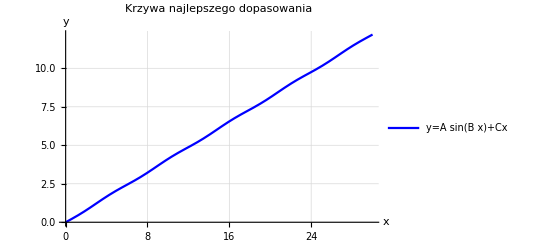

```mathematica
plotFit=Plot[fit[x],{x,0,30}, PlotStyle->{Blue},AxesLabel->{x,y},PlotLabel->Style["Krzywa najlepszego dopasowania",FontSize->26],LabelStyle->{FontSize->16},GridLines->Automatic, PlotLegends->Placed[LineLegend[{Blue},{TraditionalForm[HoldForm[y = A  Sin[B x ] + Cx]]}],Below],ImageSize->Full]
```

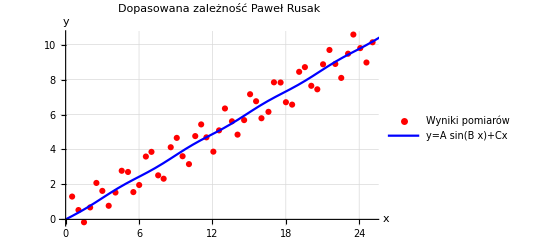

```mathematica
plotAll = Show[plotData,plotFit, AxesLabel->{x,y},PlotLabel->Style["Dopasowana zależność Paweł Rusak",FontSize->26],LabelStyle->{FontSize->16}, GridLines->Automatic, ImageSize->Full]
```

```mathematica
Export["zad3.pdf", plotAll]
```

zad3.pdf